```mathematica
data=Import[NotebookDirectory[]<>"..//images//20191228//Imgstatistics.txt","Table","FieldSeparators"->","];
desc=First[data];
time=DateObject[{ToExpression[#⟦3⟧],DateValue[#⟦2⟧,"Month"],ToExpression[#⟦1⟧],ToExpression[#⟦4⟧],ToExpression[#⟦5⟧],ToExpression[#⟦6⟧]}&@StringSplit[data⟦2⟧,{" ",":","."}]⟦1,-6;;-1⟧];
data=data⟦3;;⟧;
```

```mathematica
desc
time
```

{# 1st line:time difference in hrs to start of night exposure, 2nd line:step time difference in hrs between consecutive exposures, 3rd line:mean of image, 4th line:StdDev of image, 5th line:Focus of image}

Sat 28 Dec 2019 20:04:23GMT+1.

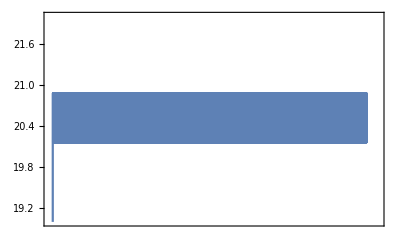

```mathematica
DateListPlot[{DatePlus[time,#]&/@(First[data]/24),3600data⟦2⟧}ᵀ,PlotRange->{{{2019,12,28,20,00,0},{2019,12,29,07,30,0}},{19,22}}]
```